## Generazione dati

```mathematica
(* setup *)
ftrue[x_]:=x(1+0.5(1+E^(-x))^(-1)); (* modello "vero" dal quale si generano i dati *)
atrue=1;
btrue=0.5;
fmod[x_,a_,b_]:=x(1+b(1+E^(-a x))^(-1));
loss[x_,y_,a_,b_]:=(y -fmod[x,a,b])^2; (* questa è solo la parte quadratica, senza somma o normalizzazione*)
gradloss[x_,y_,a_,b_]:={D[(y -fmod[x,a,b])^2,a],D[(y -fmod[x,a,b])^2,b]} ;
(* generate a sample from ftrue*)
nn=30;
ll=20;
ntot=nn ll; (*number of datapoints*)
xs = Table[xi-Floor[nn/2],{ xi,1,nn}];
fi=Table[N[ftrue[x/.(x->xs[[i]])]],{i,1,Length[xs]}];
eps=3;
epss = RandomReal[{-eps,eps},ll*Length[fi]];
data=Table[{xs[[i]],Table[fi[[i]]+epss[[i+j]],{j,0,ll-1}]},{i,1,Length[fi]}];

(******genero dati per l'errore di generalizzazione************)
nnp= Floor[N[nn/5]];
llp = Floor[N[ll/5]];
ntotp=nnp llp; (*number of datapoints*)
xsp = Table[xi-Floor[nnp/2],{ xi,1,nnp}];
fip=Table[N[ftrue[x/.(x->xsp[[i]])]],{i,1,Length[xsp]}];
epssp = RandomReal[{-eps,eps},llp*Length[fip]];
datap=Table[{xsp[[i]],Table[fip[[i]]+epssp[[i+j]],{j,0,llp-1}]},{i,1,Length[fip]}];
lossp[a_,b_]:=(1/ntotp)*Sum[ Sum[(datap[[i,2]][[j]]-fmod[datap[[i,1]],a,b])^2,{j,1,llp}],{i,1,nnp}];(*loss function per il validation set*)
(************************************************************)
```

## Visualizzo il minimo positivo per vedere se è buono

-Graphics3D-

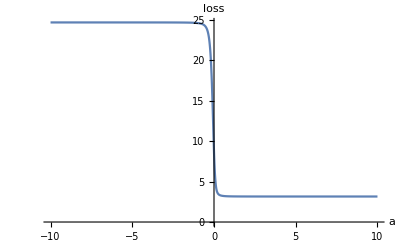

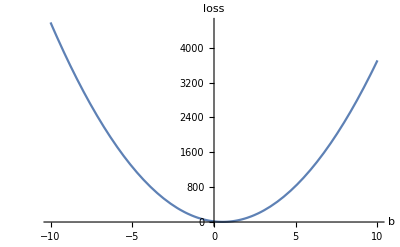

areal, breal: 1.49999 0.527108

```mathematica
(*calcolo la loss function su tutto il set di dati, in funzione dei parametri*)
loss[a_,b_]:=(1/ntot)* Sum[ Sum[(data[[i,2]][[j]]-fmod[data[[i,1]],a,b])^2,{j,1,ll}],{i,1,nn}];

(*Trovo ilm minimo reale della funzione*)
areal=x/.Last[ FindMinimum[{loss[x,y],Abs[x]<1.5 &&Abs[y]<1},{x,y}]];
breal=y/.Last[ FindMinimum[{loss[x,y],Abs[x]<1.5 &&Abs[y]<1},{x,y}]];

l=10;
Plot3D[loss[a,b],{a,-l,l},{b,-l,l}, AxesLabel->{"a","b"}]
Plot[loss[a,breal],{a,-l,l}, AxesLabel->{"a","loss"}]
Plot[loss[areal,b],{b,-l,l}, AxesLabel->{"b","loss"}]
Print["areal, breal: ", areal," ",breal]
```

## Cerco il minimo negativo per verificare il crossing

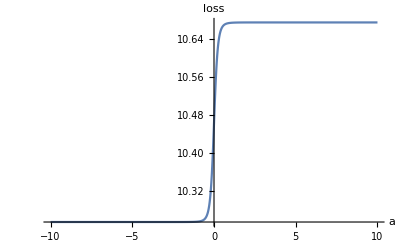

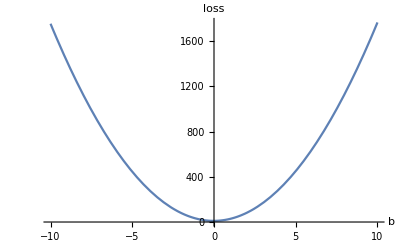

arealmin, brealmin: -2.73666 -0.0164273

```mathematica
(*Trovo ilm minimo negativo della funzione*)
arealmin=x/.Last[ FindMinimum[{loss[x,y],x<0 &&Abs[y]<1},{x,y}]];
brealmin=y/.Last[ FindMinimum[{loss[x,y],x<0 &&Abs[y]<1},{x,y}]];
Plot[loss[a,brealmin],{a,-l,l}, AxesLabel->{"a","loss"}]
Plot[loss[arealmin,b],{b,-l,l}, AxesLabel->{"b","loss"}]
Print["arealmin, brealmin: ", arealmin," ",brealmin]
```

## Genero il punto di partenza

```mathematica
a0 =RandomReal[];
b0=RandomReal[];
Print["a0, b0: ", a0," ",b0]
```

a0, b0: 0.699438 0.21897

## Training tramite SGD

```mathematica
(* IPERPARAMETRI DEL SGD *)
maxite =60000;
eta =0.0001;
bsize =10;

(* costruisco il vettore dei parametri che ottimizzo, tengo tutti le iterazioni per la visualizzazione *)
v = Table[{0,0},{ite,1,maxite}];
lossvalues=Table[0,{ite,1,maxite}]; (* per visualizzazione *)
totlossvalues=Table[0,{ite,1,maxite}]; (* sarebbe la loss usata nel GD *)
v[[1]]={a0,b0};
(* SGD loop **************************************************************)
(* nota: faccio il caso semplice del ciclo for, si può sostituire con un while per controllare se sta raggiungendo la convergenza *)
For[ite=2,ite<=maxite, ite++,
If[Mod[ite,10000]==0, Print["ite: ",ite, "/ ", maxite]];
ai = v[[ite-1]][[1]];
bi= v[[ite-1]][[2]];

(* sceglie il nuovo minibatch *)
xidxs =RandomInteger[{1,nn},bsize];
yidxs=RandomInteger[{1,ll},bsize]; (* nota che si fa così solo per il modo in cui ho costruito i dati, in generale non devi scegliere x e y in maniera indipendente!*)
xis =Table[ data[[xidxs[[bidx]],1]], {bidx,1,bsize}];
yis = Table[data[[xidxs[[bidx]],2]][[yidxs[[bidx]] ]],{bidx,1,bsize}];


(* solo per visualizzazione; calcolo la loss function per il minibatch *)  
lossvalues[[ite]]= 1/bsize 
 Sum[
N[loss[xis[[bidx]],yis[[bidx]], ai,bi]],
{bidx,1,bsize}
];

(* calcola il gradiente medio della loss rispetto ai parametri *) 
gradlossvector= 1/bsize 
 Sum[
(gradloss[xis[[bidx]],yis[[bidx]], z1,z2]/.{z1->ai,z2->bi}),
{bidx,1,bsize}
];

(* calcola l'incremento *)
dai =eta gradlossvector[[1]];
dbi =eta gradlossvector[[2]];
v[[ite]]={ai-dai, bi-dbi};
If[Mod[ite,10000]==0, Print[v[[ite]]]];
]
```

ite: 10000/ 60000

{0.558515,0.456071}

ite: 20000/ 60000

{0.284902,0.491055}

ite: 30000/ 60000

{0.221513,0.512857}

ite: 40000/ 60000

{0.22117,0.512906}

ite: 50000/ 60000

{0.226919,0.523164}

ite: 60000/ 60000

{0.220576,0.528852}

## Training tramite SDE

```mathematica
etasgd =eta;
timestep=etasgd;
maxtimes=2000;
bsizesgd =bsize;
vc = Table[{0,0},{ite,1,maxtimes}];
vc[[1]]={a0,b0};



(*calcolo l'hessiano, lo valuto su tutto il set e nel punto di minimo nello spazio dei parametri(che conosco)*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};


(*vauluto l'hessiano nel minimo reale*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
sqrthesslossmin=MatrixPower[ hesslossmin, 1/2];
Print[N[hesslossmin],"*"];
Print[Eigenvalues[hesslossmin],"*"];
Print[N[sqrthesslossmin]];

(*calcolo il gradiente su tutto il set di dati*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b}

(*calcolo la dinamica*)
For[ite=2,ite≤maxtimes, ite++,
Z={RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]};
Zscale= sqrthesslossmin.Z;
ai = vc[[ite-1]][[1]];
bi= vc[[ite-1]][[2]];
vc[[ite]][[1]]= ai-gradlosstot[x,y][[1]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[1]]*Sqrt[timestep]/.{x->ai,y->bi};
vc[[ite]][[2]]= bi-gradlosstot[x,y][[2]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[2]]*Sqrt[timestep]/.{x->ai,y->bi};
If[Mod[ite,100]==0, Print[vc[[ite]]]];
]
```

{{4029.26,3501.94},{3501.94,7774.29}}*

{9872.91,1930.64}*

{{58.5838,24.4376},{24.4376,84.7177}}

{0.67523,0.253191}

{0.656923,0.319279}

{0.678835,0.479854}

{0.655931,0.487923}

{0.696033,0.474592}

{0.674491,0.430409}

{0.751279,0.498096}

{0.712526,0.494512}

{0.748424,0.452026}

{0.772238,0.444802}

{0.764791,0.467813}

{0.754756,0.46574}

{0.805475,0.512274}

{0.76584,0.524024}

{0.747939,0.383161}

{0.755005,0.367385}

{0.793607,0.354091}

{0.810144,0.438985}

{0.83462,0.501764}

{0.84082,0.537969}

```mathematica
(************Calcolo la dinamica del GD*******************************************)
(*maxite2=1002;
vgd = Table[{0,0},{ite,1,maxite2}];
vgd[[1]]={a0,b0};
For[ite=2,ite<=maxite2, ite++,
ai = vgd[[ite-1]][[1]];
bi= vgd[[ite-1]][[2]];

(* calcola l'incremento *)
dai =eta gradlosstot[x,y][[1]]/.{x->ai,y->bi};
dbi =eta gradlosstot[x,y][[2]]/.{x->ai,y->bi};
vgd[[ite]]={ai-dai, bi-dbi}
]*)
```

## Correnti di probabilità

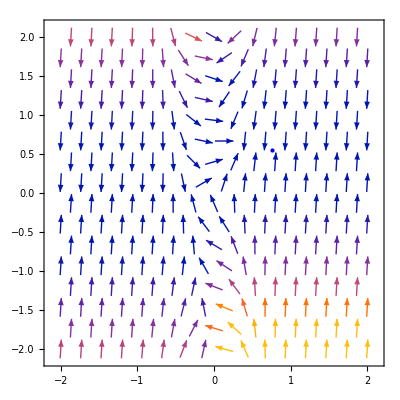

```mathematica
U[a_,b_]:= Log[loss[x,y]]/.{x->a,y->b};
T= 100;
Pstat[a_,b_]:=Exp[-U[x,y]/T]*loss[x,y]/.{x->a,y->b}; 
partialx[a_,b_]:=-D[loss[x,y],x]*Pstat[x,y]-(eta)/(bsize)*(hesslossmin[[1]][[1]]*D[loss[x,y]*Pstat[x,y],x]+hesslossmin[[1]][[2]]*D[loss[x,y]*Pstat[x,y],y])/.{x->a,y->b};
partialy[a_,b_]:=-D[loss[x,y],y]*Pstat[x,y]-(eta/bsize)*(hesslossmin[[2]][[1]]*D[loss[x,y]*Pstat[x,y],x]+hesslossmin[[2]][[2]]*D[loss[x,y]*Pstat[x,y],y])/.{x->a,y->b};


J[a_,b_]:={partialx[x,y],partialy[x,y]} /.{x->a,y->b};
r=2;
vplot=VectorPlot[J[a,b],{a,-r,r}, {b,-r,r}];
g=Graphics[{PointSize[Large],Blue,Point[{areal,breal}]}];
Show[vplot,g]
```

## Confronto i due algoritmi

parametri stimati, SGD: {0.220576,0.528852}

parametri stimati, SDE: {0.84082,0.537969}

a0, b0: 0.699438 0.21897

atrue, btrue: 1 0.5

areal, breal: 0.222361 0.520153

In-sample error, SGD: 2.55216

In-sample error, SDE: 2.8514

Out-of-sample error, SGD: 1.72075

Out-of-sample error, SDE: 1.98506

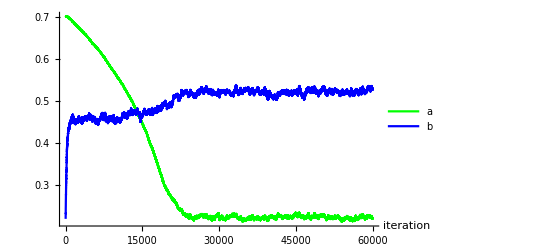

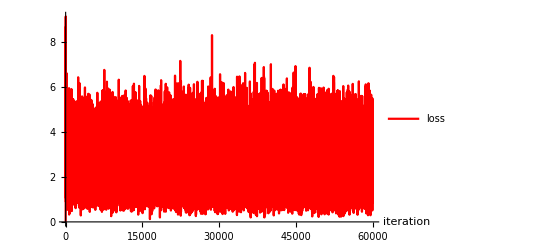

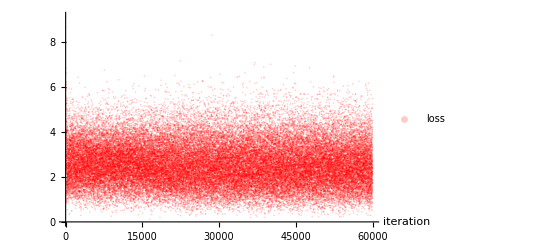

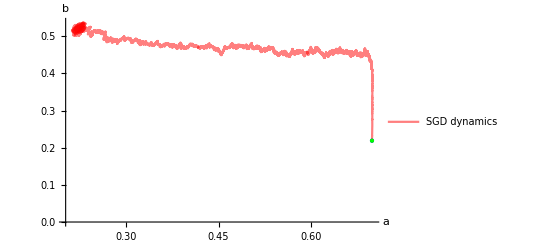

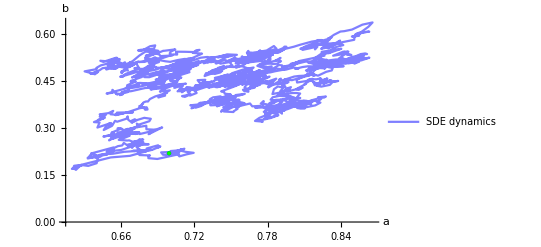

```mathematica
(* risultato: stima finale per a,b e confronto con quelli del modello vero *) 
Print["parametri stimati, SGD: ", v[[-1]]]
Print["parametri stimati, SDE: ", vc[[-1]]]
(*Print["parametri stimati, GD: ", vgd[[-1]]]*)
Print["a0, b0: ", a0," ",b0]
Print["atrue, btrue: ", atrue," ",btrue]
Print["areal, breal: ", areal," ",breal]
insamplesgd = loss[x,y]/.{x->v[[-1]][[1]],y->v[[-1]][[2]]};
(*insamplegd = loss[x,y]/.{x->vgd[[-1]][[1]],y->vgd[[-1]][[2]]};*)
insamplesde = loss[x,y]/.{x->vc[[-1]][[1]],y->vc[[-1]][[2]]};

outsamplesgd = lossp[x,y]/.{x->v[[-1]][[1]],y->v[[-1]][[2]]};
(*outsamplegd = lossp[x,y]/.{x->vgd[[-1]][[1]],y->vgd[[-1]][[2]]};*)
outsamplesde = lossp[x,y]/.{x->vc[[-1]][[1]],y->vc[[-1]][[2]]};

Print["In-sample error, SGD: ", insamplesgd," "]
(*Print["In-sample error, GD: ", insamplegd," "]*)
Print["In-sample error, SDE: ", insamplesde," "]

Print["Out-of-sample error, SGD: ", outsamplesgd," "]
(*Print["Out-of-sample error, GD: ", outsamplegd," "]*)
Print["Out-of-sample error, SDE: ", outsamplesde," "]

(* nei plot ricordati di mettere i nomi degli assi, le unità di misura se servono ecc. *)
Show[
ListLinePlot[Table[{ite,v[[ite]][[1]]},{ite,1,maxite}],
AxesOrigin->{0,0},
AxesLabel->{"iteration",""} ,PlotLegends->{"a"},PlotStyle->{Green}],
ListLinePlot[Table[{ite,v[[ite]][[2]]},{ite,1,maxite}],AxesOrigin->{0,0},
PlotLegends->{"b"},PlotStyle->{Blue}],PlotRange->All
]



ListLinePlot[Table[{ite,lossvalues[[ite]]},{ite,1,maxite}],PlotLegends->{"loss"},PlotStyle->{Red},
AxesLabel->{"iteration",""},PlotRange->All]

ListPlot[Table[{ite,lossvalues[[ite]]},{ite,1,maxite}],PlotLegends->{"loss"},PlotStyle->{Red,Opacity[0.2]},
AxesLabel->{"iteration",""},PlotRange->All]

initial=Graphics[{PointSize[Large],Green,Point[{a0,b0}]}]; (*punto di partenza*)
psgd=ListLinePlot[Table[{v[[ite]][[1]],v[[ite]][[2]]},{ite,1,maxite}],PlotLegends->{"SGD dynamics"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[psgd,g,initial]

psde=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,1,maxtimes}],PlotLegends->{"SDE dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[psde,g,initial]

(*ListLinePlot[Table[{vgd[[ite]][[1]],vgd[[ite]][[2]]},{ite,1,maxtimes}],PlotLegends->{"GD dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All]*)
```